```mathematica
faces=Transpose[{{Sqrt[3],0,-Sqrt[3],-Sqrt[3],0,Sqrt[3]},{1,1,1,-1,-1,-1},{-2d,-d,-2d,-2d,-d,-2d}{1.1,0.9,1.5,0.9,1.7,1.2}}/.{d->Sqrt[3]/2,h->0.3}]
```

{{√3,1,-1.90526},{0,1,-0.779423},{-√3,1,-2.59808},{-√3,-1,-1.55885},{0,-1,-1.47224},{√3,-1,-2.07846}}

```mathematica
vtx=Select[({x,y}/.#[[1]]&)/@Select[Solve[(#==0&)/@#,{x,y}]&/@(#.{x,y,1}&/@Subsets[faces,{2}]),Length@#>0&],AllTrue[Chop[faces.Append[#,1]],#≤0.0&]&]//DeleteDuplicates
```

{{0.65,0.779423},{1.15,-0.0866025},{-1.05,0.779423},{-1.2,0.519615},{-0.05,-1.47224},{0.35,-1.47224}}

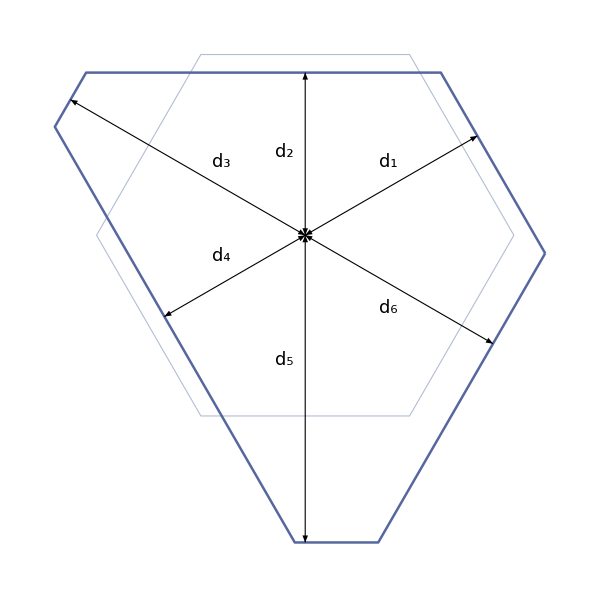

```mathematica
Graphics[{{EdgeForm[Directive[Dashed,ColorData[2,6]]],FaceForm[None],Polygon@Table[{Cos[q],Sin[q]},{q,0,2Pi,Pi/3}]},{EdgeForm[Directive[AbsoluteThickness[1.8],ColorData[2,9]]],FaceForm[None],Polygon@vtx[[{2,1,3,4,5,6}]]},{AbsoluteThickness[0.8],Arrowheads[{-.025,.025}],Arrow[{{0,0},#}]&/@((Normalize/@faces[[All,1;;2]]){1.1,0.9,1.5,0.9,1.7,1.2}Sqrt[3]/2)},{Text[Style[#1,18,FontFamily->"Times New Roman",Italic],#2]&@@@{{"d_1",{.4,.35}},{"d_2",{-.1,.4}},{"d_3",{-.4,.35}},{"d_4",{-.4,-.1}},{"d_5",{-.1,-.6}},{"d_6",{.4,-.35}}}}},ImageSize->600]
```

```mathematica
faces=With[{d={1,1.5,0.8,1,1.7,1}Sqrt[3]/2.0},Transpose[{{Sqrt[3],0,-Sqrt[3],-Sqrt[3],0,Sqrt[3],Sqrt[3],0,-Sqrt[3],-Sqrt[3],0,Sqrt[3],Sqrt[3],0,-Sqrt[3],-Sqrt[3],0,Sqrt[3],0,0},{1,1,1,-1,-1,-1,1,1,1,-1,-1,-1,1,1,1,-1,-1,-1,0,0},{0,0,0,0,0,0,a0,a0/2,a0,a0,a0/2,a0,-a0,-a0/2,-a0,-a0,-a0/2,-a0,1,-1},dCoef}/.dCoef->(({-2,-1,-2,-2,-1,-2}d)~Join~({-2,-1,-2,-2,-1,-2}(d+b0/2))~Join~({-2,-1,-2,-2,-1,-2}(d+b0/2))~Join~{-h2-h1,-h2-h3})/.{b0->a0 h2}/.{a0->Sqrt[3]/1.69,h1->0.3,h2->0.2,h3->1.2}]];
```

```mathematica
vtx=Select[({x,y,z}/.#[[1]]&)/@Select[Solve[(#==0&)/@#,{x,y,z}]&/@(#.{x,y,z,1}&/@Subsets[faces,{3}]),Length@#>0&],AllTrue[Chop[faces.Append[#,1]],#≤0.0&]&]//Chop//DeleteDuplicates;
```

```mathematica
Length@vtx
```

24

```mathematica
DirectionalVectorAngle[v1_,v2_,n_]:=Block[{s,c},c=Dot[v1,v2]/Norm[v1]/Norm[v2];s=Dot[Cross[v1,v2],n]/Norm[v1]/Norm[v2]/Norm[n];ArcTan[c,s]]
```

```mathematica
ptsNormal=({Sort@vtx[[#[[All,1]]]],faces[[#[[1,2]],1;;3]]}&/@SortBy[GatherBy[Position[faces.Append[#,1]&/@vtx//Chop,0],Last],#[[1,2]]&]);
```

```mathematica
polygons=Function[{vs,n},{SortBy[vs,DirectionalVectorAngle[vs[[1]]-Mean[vs],#-Mean[vs],n]&],n}]@@@ptsNormal;
```

```mathematica
g=With[{vp={.45,2.4,1.}2.5,vc={0,0,1.}2.5,vv={0,0,1}},Block[{visibleFaces,invisibleFaces},{visibleFaces,invisibleFaces}=GatherBy[polygons,AllTrue[#[[1]].#[[2]]-vp.#[[2]],Positive]&];Graphics3D[{{Arrowheads[{{.02}}],AbsoluteThickness[1.3],MapThread[Arrow[{#1,#2}]&,{-IdentityMatrix[3]{1.2,1.8,1.9},IdentityMatrix[3]{1.5,2.0,1.2}}]},{FaceForm[None],EdgeForm[Directive[ColorData[2,9],Dashing[.01{1,3}],AbsoluteThickness[1.0]]],Polygon@invisibleFaces[[All,1]]},{FaceForm[Opacity[.8]],EdgeForm[Directive[ColorData[2,9],AbsoluteThickness[2.5]]],Polygon@visibleFaces[[All,1]]},(*{EdgeForm[None],FaceForm[Opacity[.7]],Table[{Texture[Rasterize[Style[StringTemplate["  ``  "][i],ColorData[2,9]],RasterSize->200,ImageSize->100]],Polygon[polygons[[i-2,1]],VertexTextureCoordinates->{{0,1},{0,0},{1,0},{1,1}}]},{i,{6,7,8}}],Table[{Texture[Rasterize[Style[StringTemplate["  ``  "][i],ColorData[2,9]],RasterSize->200,ImageSize->100]],Polygon[polygons[[i-2,1]],VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},{i,{3,4,5}}]},*)(*{AbsoluteThickness[0.8],Line[{#,#{0,1,1}+{-1.8,0,0}}]&/@Extract[polygons[[{9,15},1]],{{1,3},{2,2}}],Line[{#,#{0,1,1}+{-1.8,0,0}}]&/@polygons[[3,1,2;;3]],Line[{#,#+{0,0,1.1}}]&/@Extract[polygons[[{1,3},1]],{{1,4},{2,3}}],Arrowheads[{-.015,.015}],Arrow[{#1{0,1,1}+{-1.7,0,0},#2{0,1,1}+{-1.7,0,0}}]&@@polygons[[3,1,2;;3]],Arrow[{#1{0,1,1}+{-1.7,0,0},#2{0,1,1}+{-1.7,0,0}}]&@@polygons[[9,1,2;;3]],Arrow[{#1{0,1,1}+{-1.7,0,0},#2{0,1,1}+{-1.7,0,0}}]&@@polygons[[15,1,2;;3]],Arrow[{#1{1,1,0}+{0,0,1.2},#2{1,1,0}+{0,0,1.2}}]&@@Extract[polygons[[{1,3},1]],{{1,4},{2,3}}]},*){Text[Style[#1,FontFamily->"Times New Roman",18,Italic],#2]&@@@{{"x",{1.6,0,0}},{"y",{-.05,2.0,0}},{"z",{-.1,0,1.2}}}}},Boxed->False,ViewVector->{vp,vc-vp},ViewVertical->vv,Lighting->{{"Ambient", White}},ImageSize->600]]]
```

-Graphics3D-